# Boosting GPS State Generation Rate

The GPS success probabiity, as a function of input squeezing (r) and number of photons detected (n) is given by PGPS.

```mathematica
PGPS = (2^-n Cosh[2 r]^(-1/2-n) (2 n)! Sinh[r]^(2 n))/(n!)^2;
```

For a given number of detected photons, the squeezing that gives maximum PGPS is rMax.

```mathematica
rMax = 1/2*ArcSech[1/(1+2*n)];
PGSMax = PGPS/.r->rMax;
```

For a given number of detected photons, the optimal input squeezing, to get a state with peaks at q = +- Sqrt[2 Pi] , is rOpt.

```mathematica
rOpt = 1/2*ArcSech[(2*Pi)/n];
PGPSOpt = PGPS/.r->rOpt;
```

Plots

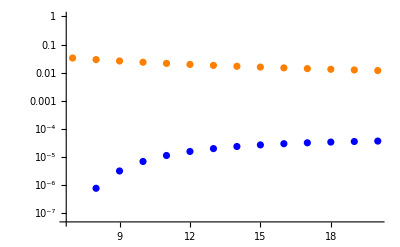

```mathematica
nSpace= Range[7,20];
PGPSMaxTable = Table[{nSpace[[ii]],PGSMax/.n->nSpace[[ii]]},{ii,1,Length[nSpace]}];
PGPSOptTable = Table[{nSpace[[ii]],PGPSOpt/.n->nSpace[[ii]]},{ii,1,Length[nSpace]}];
PlotPGPSMax = ListLogPlot[PGPSMaxTable,PlotStyle->Orange,PlotRange->{5*10^-8,1}];
PlotPGPSOpt = ListLogPlot[PGPSOptTable,PlotStyle->Blue,PlotRange->{5*10^-8,1}];
Show[PlotPGPSOpt,PlotPGPSMax]
```